# Sphere Packing Ben Nissan and Tom Magerlein

## Distribute particles randomly on a sphere and set initial parameters

First we declare the number of particles we plan to pack.

```mathematica
numParticles = 12;
```

Next, we generate random coordinates (ranging from -1 to 1 on x, y, and z) for each particle and normalize them to fit to the unit sphere on which we are packing.  To do so, we generate a list of random unit vectors and set each one’s components as the coordinates of one of our points.

```mathematica
randUnitVec := Normalize[{2Random[] -1, 2Random[] - 1, 2Random[] - 1}];
```

```mathematica
xRand = Table[randUnitVec,{i,numParticles}];
```

```mathematica
x0 = Map[#/Norm[#]&,xRand];
```

We set the initial radius of each particle to some relatively small value—say, 0.01.

```mathematica
r0 = Table[0.01,{i,numParticles}];
```

Let’s visualize the particles to verify their random distribution on the sphere.

```mathematica
showParticles[x_,r_]:=Graphics3D[Join[{Green},Table[Sphere[x[[i]],r[[i]]],{i,Length[x]}],{Gray,Sphere[{0,0,0}]}],Boxed->False];
```

```mathematica
showParticles[x0,r0]
```

-Graphics3D-

The particles appear to be randomly distributed, which is ideal.

## Moving along the sphere

Next, we create a function to randomly shift a particle along the surface of the sphere by some small amount.

```mathematica
shift[x_,δ_]:=Block[{dx,xNew},

(* Generates a random magnitude and direction for our initial shift *)
dx = RandomVariate[ NormalDistribution[0,δ]] * randUnitVec;

(* dx is currently in a completely random direction, which we need to fix so that our particle moves along the sphere's surface.  Because the local vector normal to the sphere at point x is parallel to vector x, we can subtract from dx the component parallel to vector x to force dx tangent to the sphere, a good first start. *)
dx-=(dx.x) x/(x.x);

(* Now, we shift x. *)
xNew = x + dx;

(* Finally, we reproject our new position onto the surface of the sphere and return the corrected position. *)
xNew /= Sqrt[xNew . xNew];

Return[xNew]

]
```

We can test this by running it multiple times on a point with arbitrary initial position and logging its movement over many iterations.  Ideally, this will produce a random path.

```mathematica
testx0 = {1,0,0};
randPath := Reap[Do[Sow[testx0=shift[testx0,0.03]],{i,1000}]];
Graphics3D[{Gray,Sphere[{0,0,0},1],Green,Line[randPath⟦2,1⟧]},Boxed-> False]
```

-Graphics3D-

And we see a nice random path.

## Shifting multiple particles

When moving multiple different particles along the same sphere, we need to make sure that none of them crash into each other or overlap.  We create a function to check, for each particle in a given list of coordinates, whether a desired shift is possible, shift the particle if so, and report whether the shift was successful.

```mathematica
checkAndShift[coords_,radii_,δ_]:=Block[{newCoords=coords,oldCoord,nearest,success=0,order,current},

(* For each particle in the list, selecting in random order: *)
order = RandomSample[Range[Length[coords]]];

Do[
(* We store our current position and generate a new one. *)
current = order⟦i⟧;
oldCoord=newCoords⟦current⟧;
newCoords⟦current⟧=shift[newCoords⟦current⟧,δ];

(* Then, we find the index of the nearest particle. *)
nearest=Last[Nearest[MapIndexed[#-> #2⟦1⟧&,newCoords],newCoords⟦current⟧,2]];

(* If the move results in a collision, we reject it. *)
Do [If[Norm[newCoords⟦current⟧-newCoords⟦nearest⟧]<radii⟦current⟧+radii⟦nearest⟧,newCoords⟦current⟧=oldCoord; Break[],success++],
{i,10}
]
(* And we iterate over the entire list. *)
,{i,Length[coords]}];

Return[{newCoords,success}]

]
```

Let’s test this on a fairly small list of fairly large particles over a large number of iterations.

```mathematica
testRadii = Table[0.4, {i, Length[x0]}];
testx0b = x0;
testPaths := Reap[Do[Sow[testx0b=checkAndShift[testx0b,testRadii,0.1]⟦1⟧],{i,100}]];
```

```mathematica
Graphics3D[Join[{Gray,Sphere[{0,0,0}]},Table[{Hue[i/Length[testx0b]],Line[Transpose[testPaths⟦2,1⟧]⟦i⟧]},{i,Length[testx0b]}]],Boxed-> False]
```

-Graphics3D-

## Packing the particles

Now that we can maneuver the particles around each other without collisions, we can pack!  We do so by writing a function that, over many iterations, does the following in each:
First, it calls checkAndShift on our list of particles, noting the ratio of successful moves to unsuccessful moves.  If the ratio is greater than zero, it inflates the particles by a small amount (much smaller than the distance we move them in checkAndShift) and proceds to the next iteration.  If the ratio is zero, then the particles are fully packed and the function exits.

We set our initial shift length and pack!

```mathematica
δ0 = 0.03;
```

```mathematica
pack[r0_,x0_,δ0_]:=Block[{rCurrent = r0, xCurrent = x0, δCurrent = δ0,ratios,currentRatio},
ratios = Reap[Do[

(* Shifts the particles. *)
{xCurrent,currentRatio}=checkAndShift[xCurrent,rCurrent,δCurrent];

(* Logs the number of moves accepted *)
Sow[currentRatio/Length[xCurrent]];

(* Stops if the acceptance ratio hits zero. *)
If[currentRatio==0,Break[]];

(* Inflates the particles otherwise. *)
rCurrent=Map[#+0.0005&,rCurrent];

,{i,2000}]];

Return[{ratios,xCurrent, rCurrent}]

]
```

We record our table of acceptance ratios, our final particle positions, and their final radii.

```mathematica
packResults = pack[r0,x0,δ0];
ratioResults = packResults⟦1⟧;
xResults = packResults⟦2⟧;
rResults = packResults⟦3⟧;
```

We plot the acceptance ratios:

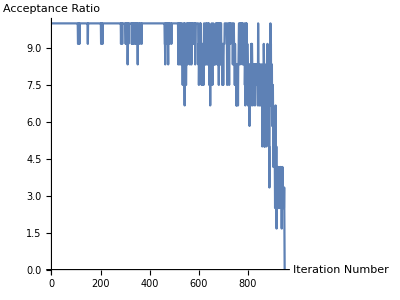

```mathematica
ListPlot[ratioResults⟦2,1⟧,Joined->True,AxesLabel->{"Iteration Number","Acceptance Ratio"},AspectRatio->3/4]
```

And, finally, show off our packed particles!

```mathematica
Show[showParticles[xResults,rResults],Boxed->False]
```

-Graphics3D-